```mathematica
FullSimplify[Solve[{E^(g+k2)==2(E^-k+E^k Cosh[4k]),E^(g-k2)==4Cosh[k]},{g,k2}]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{g→1/2 (Log[Cosh[k]]+Log[8 (ⅇ^-k+ⅇ^k Cosh[4 k])]),k2→1/2 (-Log[4 Cosh[k]]+Log[2 (ⅇ^-k+ⅇ^k Cosh[4 k])])}}

```mathematica
FullSimplify[D[(E^-k+E^k Cosh[4k])/(2Cosh[k]),k]]
```

2 (ⅇ^(4 k)-Cosh[2 k])

```mathematica
Solve[2 u^3-u^2-1==0,u]
```

{{u→1},{u→1/4 (-1-ⅈ √7)},{u→1/4 (-1+ⅈ √7)}}

```mathematica
Solve[(E^-k+E^k Cosh[4k])/(2Cosh[k])== E^(2k),k]
```

{{k→ConditionalExpression[2 ⅈ π C[1],C[1]∈ℤ]},{k→ConditionalExpression[ⅈ π+2 ⅈ π C[1],C[1]∈ℤ]},{k→ConditionalExpression[2 ⅈ π C[1]+Log[-ⅈ √(-1+√2)],C[1]∈ℤ]},{k→ConditionalExpression[2 ⅈ π C[1]+Log[ⅈ √(-1+√2)],C[1]∈ℤ]},{k→ConditionalExpression[2 ⅈ π C[1]+1/2 Log[1+√2],C[1]∈ℤ]},{k→ConditionalExpression[ⅈ π+2 ⅈ π C[1]+1/2 Log[1+√2],C[1]∈ℤ]}}

```mathematica
Solve[u^4-2 u^3-2 u^2+2 u+1==0,u]
```

{{u→-1},{u→1},{u→1-√2},{u→1+√2}}

```mathematica
Factor[u^4-2 u^3-2 u^2+2 u+1]
```

(-1+u) (1+u) (-1-2 u+u^2)

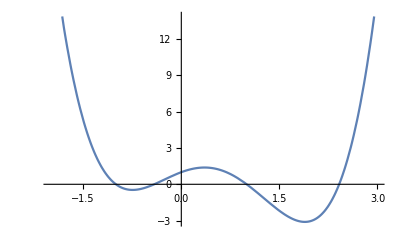

```mathematica
Plot[u^4-2 u^3-2 u^2+2 u+1,{u,-2,3}]
```

```mathematica
f[u_]:=u-(1+u^-2)/2;
FullSimplify[f[1+√2]]
```

-1+2 √2

```mathematica
N[Log[2]/Log[2 √2-1]]
```

1.14863

```mathematica
Factor[x^4-3 x^3+3x-1]
```

(-1+x) (1+x) (1-3 x+x^2)

```mathematica
Solve[(1-3 x+x^2)==0]
```

{{x→1/2 (3-√5)},{x→1/2 (3+√5)}}

```mathematica
FullSimplify[D[(t^9+3 t^3)/(3 t^6+1),t]]
```

(9 t^2 (-1+t^6)^2)/((1+3 t^6)^2)

```mathematica
g[t_]:=(9 t (-1+t^3)^2)/((1+3 t^3)^2);
FullSimplify[g[(3-√5)/2]]
```

9/4

```mathematica
N[ArcTanh[√((3-√5)/2)]]
```

0.721818

```mathematica
N[Log[1+√2]/2]
```

0.440687